```mathematica
(***************************************)
(****Scalar field equaition*************)
(***************************************)
(***************************************)
(***************Background In case!****************)
(***************************************)
w=-0.9;
cs=10^-3;
h=0.67556;c=29979.2458;
H0=100. h/c;
Omegab=0.022032/h/h;Omegacdm=0.12038/h/h;
Omegam=Omegab+Omegacdm;OmegaLambda=0.0;
Omegarad=9.16681 10^-5;Omegakessence=0.687862;
Hubb[a_]:=H0 a √(Omegam a^-3.+Omegarad  a^-4.+OmegaLambda+Omegakessence a^(-3.*(1.+w)));
LogLogPlot[Hubb[a],{a,1./(1.+100),1}];
SetDirectory[NotebookDirectory[]];
(*Eq1II=-3 H[τ] (w ζ[τ]) +ζ'[τ];*)
Eq1II=ζ'[τ];
(*Eq2II= piC'[τ]+H[τ]piC[τ];*)
Eq2II= H'[τ]piC[τ] + H[τ]piC'[τ];
Eq1I=Eq1II/.{piC->(piC[a[#]]&),ζ->(ζ[a[#]]&) };
Eq2I=Eq2II/.{piC->(piC[a[#]]&),ζ->(ζ[a[#]]&) };
a''[τ]=a[τ](H[τ]^2+H'[τ]);
a'[τ]=a[τ]H[τ];
H[τ_]:=Hubb[a[τ]];
(*Field equation in terms of scale factor!*)
Eq1:=Eq1I/.a[τ]:>a;
Eq2:=Eq2I/.a[τ]:>a;
(***************************************)
(***************IC read fromt the file***)
(***************************************)
(*Class file columns: # 1:k (h/Mpc) 2:d_kess_pi 3:t_kess_zeta 4:delta_fld 5:theta_fld 6:psi 7:delta_cdm 8:H_conf/H0 *)
data=Import["./Class_files/Class_kess_cs_e3_z100_newt_Gev.dat",{"Data",{All}}];
(*Making output file foe Gev field!*)
As=2.19 10^-9;
h=0.67556;
kp=0.05/h;
ns=0.96;
cs2=10^-6;
(*IMPORTS*)
Addr="2018.05.22.14.49.11";
datapiGev100=Cases[Import["./NewVariable_Gevolution/"<> Addr<>"/kess_pk_cs_e3_000_pi_k.dat",{"Data",{All}}],{_?NumberQ,___}];
datazetaGev100=Cases[Import["./NewVariable_Gevolution/"<> Addr<>"/kess_pk_cs_e3_000_zeta.dat",{"Data",{All}}],{_?NumberQ,___}];
dataGevphiz100=Cases[Import["./NewVariable_Gevolution/"<> Addr<>"/kess_pk_cs_e3_000_phi.dat",{"Data",{All}}],{_?NumberQ,___}];
dataGevphiprimez100=Cases[Import["./NewVariable_Gevolution/"<> Addr<>"/kess_pk_cs_e3_000_phi_prime.dat",{"Data",{All}}],{_?NumberQ,___}];

datapiGev50=
Cases[Import["./NewVariable_Gevolution/"<> Addr<>"/kess_pk_cs_e3_001_pi_k.dat",{"Data",{All}}],{_?NumberQ,___}];
datazetaGev50=Cases[Import["./NewVariable_Gevolution/"<> Addr<>"/kess_pk_cs_e3_001_zeta.dat",{"Data",{All}}],{_?NumberQ,___}];
```

Import::nffil: File not found during Import.

```mathematica
Dimensions[datapiGev100]
```

{843,5}

```mathematica
datapiGev100
```

{843,5}

```mathematica
(*datapiGev10=
Cases[Import["./NewVariable_Gevolution/"<> Addr<>"/kess_pk_cs_e3_004_pi_k.dat",{"Data",{All}}],{_?NumberQ,___}];
datazetaGev10=Cases[Import["./NewVariable_Gevolution/"<> Addr<>"/kess_pk_cs_e3_004_zeta.dat",{"Data",{All}}],{_?NumberQ,___}];
*)(*z=10*)
(*dataGevphiprimez10=Import["./NewVariable_Gevolution/output_1_128/kess_pk_cs_e3_004_phi_prime_z10.dat",{"Data",{All}}]*)
(*dataGevphiz10=Import["./NewVariable_Gevolution/output_1_128/kess_pk_cs_e3_004_phi_z10.dat",{"Data",{All}}];*)


GevFieldz100=√(datapiGev100[[All,2]]/(As (datapiGev100[[All,1]]/kp)^(ns-1)));

Gevzetaz100=√(datazetaGev100[[All,2]]/(As (datazetaGev100[[All,1]]/kp)^(ns-1)));

Gevphiprimez100=√(dataGevphiprimez100[[All,2]]/(As (dataGevphiprimez100[[All,1]]/kp)^(ns-1)));
Gevphiz100=√(dataGevphiz100[[All,2]]/(As (dataGevphiz100[[All,1]]/kp)^(ns-1)));
a0=1./(1.+100.00);
a1=1./(1.+48.51);
Δa=0.00005; (*Sampling to solve ODE*)
kmax=Dimensions[datapiGev100[[All,1]]][[1]];
Agrex=Table[Table[0,{aa,1,Floor[((a1-a0)/Δa)]+1},{num,1,3}],{k,1,kmax}];
Dimensions[Agrex](*k , a , pi[a], zeta[a]*)(*For each k we have a * 3 where a is the number of a sampling and 3 is the number of columns. a pi and pi' for  *)
GevPowerDataz100=Table[{datapiGev100[[l,1]],GevFieldz100[[l]],Gevzetaz100[[l]]},{l,1,Dimensions[GevFieldz100][[1]]}];
(*GevPowerDataz50=Table[{datapiGev50[[l,1]],GevFieldz50[[l]],Gevzetaz50[[l]]},{l,1,Dimensions[GevFieldz50][[1]]}];*)

(*Agrex[[4]] //MatrixForm*)
(*phiprimez10=√(dataGevphiprimez10[[All,2]]/(As (dataGevphiprimez10[[All,1]]/kp)^(ns-1)));
Gevphiz10=√(dataGevphiz10[[All,2]]/(As (dataGevphiz10[[All,1]]/kp)^(ns-1)));*)
(*GevFieldz10=√(datapiGev10[[All,2]]/(As (datapiGev10[[All,1]]/kp)^(ns-1)));*)
GevFieldz50=√(datapiGev50[[All,2]]/(As (datapiGev50[[All,1]]/kp)^(ns-1)));
(*Gevpivz100=√(datapivGev100[[All,2]]/(As (datapivGev100[[All,1]]/kp)^(ns-1)));*)
(*Gevzetaz50=√(datazetaGev50[[All,2]]/(As (datazetaGev50[[All,1]]/kp)^(ns-1)));*)
(*Gevzetaz10=√(datazetaGev10[[All,2]]/(As (datazetaGev10[[All,1]]/kp)^(ns-1)));*)

(***************************************)
(****For each k in IC file we need to solve th e ODE numerically!***************)
(***************************************)
amaxComun=Floor[((a1-a0)/Δa)]+1;
```

{843,206,3}

```mathematica
GevPowerDataz100=Table[{datapiGev100[[l,1]],Abs[GevFieldz100[[l]]]/GevFieldz50[[l]]},{l,1,Dimensions[GevFieldz100][[1]]}];
```

```mathematica
GevPowerDataz100[[All,2]];
```

```mathematica
Sum[GevPowerDataz100[[All,2]]]
```

Sum::argmu: Sum called with 1 argument; 2 or more arguments are expected.

Sum[GevPowerDataz100⟦All,2⟧]

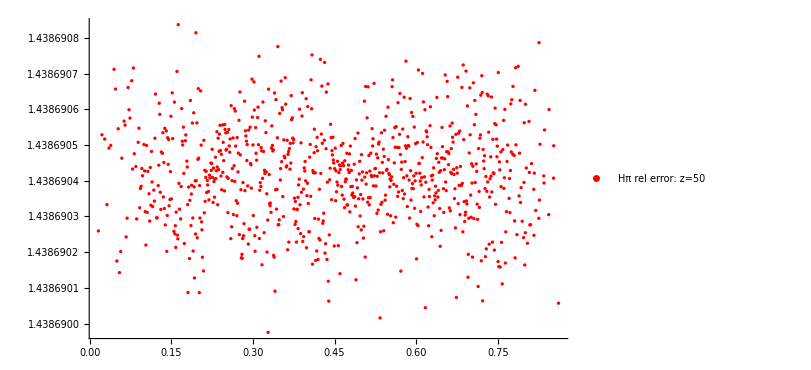

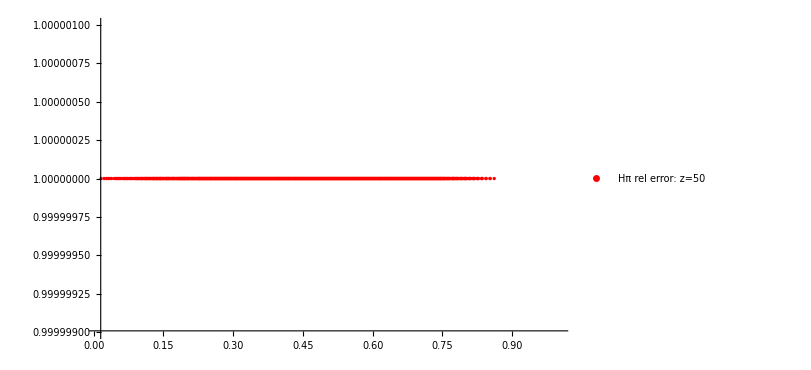

```mathematica
perrorπ50=ListPlot[GevPowerDataz100[[All,{1,2}]],PlotStyle->{Red,Line,PointSize[0.004]},PlotLegends->{" Ηπ rel error: z=50"},PlotRange->{{10^-2,1},{1.4386902591552235+10^-6.,1.4386902591552235-10^-6.}},ImageSize->600];
Show[perrorπ50]
```

```mathematica
MatSolz100=Table[{GevPowerDataz100[[k,1]],Abs[Agrex[[k]][[1,2]][[1]]],Abs[Agrex[[k]][[1,3]][[1]]]},{k,1,kmax}];
```

```mathematica
(*GevPowerDataz10=Table[{datapiGev10[[l,1]],GevFieldz10[[l]],Gevzetaz10[[l]]},{l,1,kmax}];*)
For[kk=1,kk<kmax+1,kk++,
(*k is wavenumber in the eq
The IC is set for each wavenumber accordingly!
Also \Psi is set for each k accordingly in the loop which is assumed to be constant in matter dominated universe!*)
kwave=GevPowerDataz100[[kk,1]]*h;
(*We multiply by h since the unit of k is 1/Mpc not h/Mpc! while in the file is k=[h/Mpc] *)
(*piC'[a0]==data[[kk,3]]/(Hubb[a0]a0) is IC for dπ/da*)
(*Ψ[τ]=Gevphiz100[[kk]];*)
(*Φ'[τ]=Gevphiprimez100[[kk]]Hubb[a0];*)
Ψ[τ]=0;
Φ'[τ]=0;
(*It is multiplied to Hubble since it is function of τ while after changing the variable it gets H factor*)
(*Φprime must be provided in new variable a[tau]*)
(*Φprime=Gevphiprimez21[[kk]]Hubb[a0];*)
Sol=NDSolve[{Eq1==0,Eq2==0,piC[a0]==GevPowerDataz100[[kk,2]]/Hubb[a0],ζ[a0]==GevPowerDataz100[[kk,3]]},{piC,ζ},{a,a0,a1}]; 
(*The pi field in Gevolution is divided by H since in the output it is multiplied to!*)(*Note that for the initial value of π'[a0] it is not just data[[kk,3]]/(Hubb[a0]a0) since now it is the function of "a" which gets a new coefficient by changing the variable but not for ζ which is dimensionless*)
Agrex[[kk]][[All,1]]=Table[a,{a,a0,a1,Δa}];
(*Hubb[a]piC[a] is dimensionless field,  piC'[a]Hubb[a]a is dπ/dτ according to chain rule!*)
Agrex[[kk]][[All,{2,3}]]=Table[{Hubb[a]piC[a]/.Sol, ζ [a]/.Sol},{a,a0,a1,Δa}];
(*Hubb[a]piC[a] is a dimensionless variable and ζ [a]Hubb[a]a is to change in temrs of conformal time*)
]
Agrex[[3]][[{2,7},2]]//MatrixForm; (*To check consistency!*)
(*K info is in the loaded file, and for each k we have the solution in time (pi, pi')!*)
(*Ψdata[[i,1]] is k lists! Agrex[[i]][[2,2]][[1]] is pi soluition for constant time!*)
```

```mathematica
MatSolz100=Table[{GevPowerDataz100[[k,1]],Abs[Agrex[[k]][[1,2]][[1]]],Abs[Agrex[[k]][[1,3]][[1]]]},{k,1,kmax}];
MatSolz50=Table[{GevPowerDataz50[[k,1]],Abs[Agrex[[k]][[amaxComun,2]][[1]]],Abs[Agrex[[k]][[amaxComun,3]][[1]]]},{k,1,kmax}]//N;

(*MatSolz10=Table[{GevPowerDataz10[[k,1]],Abs[Agrex[[k]][[amaxComun,2]][[1]]],Abs[Agrex[[k]][[amaxComun,3]][[1]]]},{k,1,kmax}]//N;*)
(*dataz10=
Import["./Class_files/Class_kess_cs_e3_z10_newt_Gev.dat",{"Data",{All}}];*)
Errorπ50=Table[{MatSolz50[[k,1]],Abs[(MatSolz50[[k,2]]-GevPowerDataz50[[k,2]])]/GevPowerDataz50[[k,2]]},{k,1,kmax}]//N;
Errorζ50=Table[{MatSolz50[[k,1]],Abs[(MatSolz50[[k,3]]-GevPowerDataz50[[k,3]])]/GevPowerDataz50[[k,3]]},{k,2,kmax}]//N;
Errorζ100=Table[{MatSolz100[[kl,1]],Abs[(MatSolz100[[kl,3]]-GevPowerDataz100[[kl,3]])]/GevPowerDataz100[[kl,3]]},{kl,2,kmax}]//N;
Errorπ100=Table[{MatSolz100[[km,1]],Abs[(MatSolz100[[km,2]]-GevPowerDataz100[[km,2]])]/GevPowerDataz100[[km,2]]},{km,1,kmax}]//N;
```

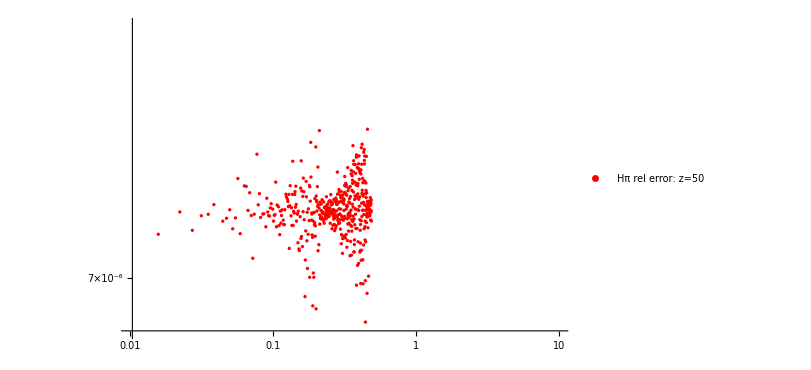

```mathematica
p1=ListLogLogPlot[MatSolz100[[All,{1,2}]],PlotStyle->{Blue,Line,PointSize[0.004]},PlotLegends->{"Solved here Ηπ: z=100"},ImageSize->900,PlotRange->{{10^-2,10},{10^-17,10^0}}];
p2=ListLogLogPlot[MatSolz50[[All,{1,2}]],PlotStyle->{Purple,Line,PointSize[0.004]},ImageSize->700,PlotLegends->{"Solved here Ηπ: z=10"}];
pGev100=ListLogLogPlot[GevPowerDataz100[[All,{1,2}]],PlotStyle->{Green,Line,PointSize[0.004]},PlotLegends->{"Gev Ηπ: z=100"},ImageSize->600];
pGev50=ListLogLogPlot[GevPowerDataz50[[All,{1,2}]],PlotStyle->{Maroon,Line,PointSize[0.004]},PlotLegends->{"Gev Ηπ: z=50"},ImageSize->600];
perrorζ50=ListLogLinearPlot[Errorζ50[[All,{1,2}]],PlotStyle->{Blue,Line,PointSize[0.004]},PlotLegends->{" ζ  rel error: z=50"},ImageSize->600];
perrorπ50=ListLogLogPlot[Errorπ50[[All,{1,2}]],PlotStyle->{Red,Line,PointSize[0.004]},PlotRange->{{10^-2,10},{0.68 10^-5,0.8 10^-5}},PlotLegends->{" Ηπ rel error: z=50"},ImageSize->600];
Show[perrorπ50]
```

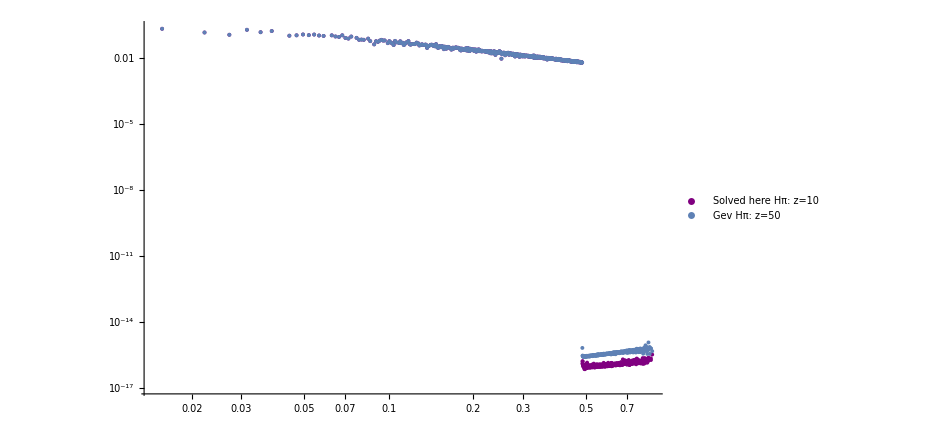

-Graphics-

```mathematica
Show[p2,pGev50]
Show[perrorπ50]
```

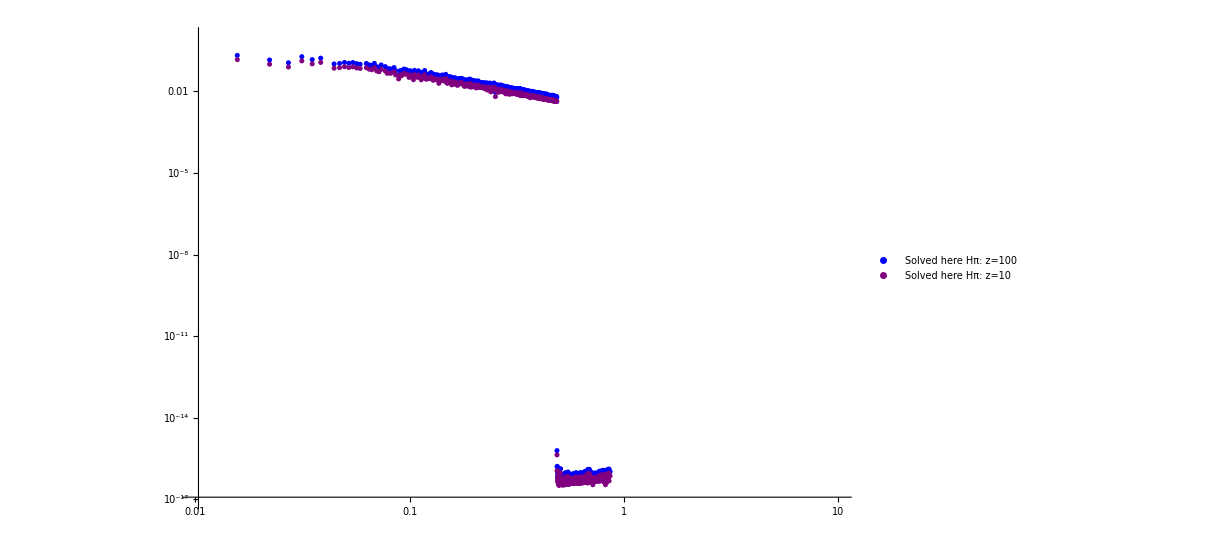

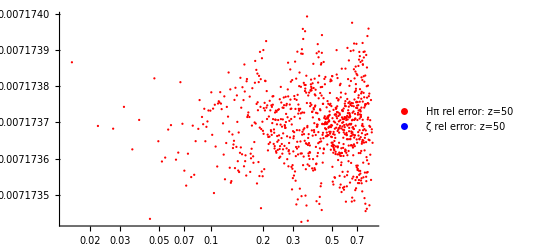

```mathematica
(*pζ1=ListLogLogPlot[MatSolz100[[All,{1,3}]],PlotStyle->{Black,Line,PointSize[0.004]},PlotLegends->{"Solved here ζ: z=100"},ImageSize->900,PlotRange->{{10^-2,10},{10^-12,10^-2}}];
pζ2=ListLogLogPlot[MatSolz50[[All,{1,3}]],PlotStyle->{Red,Line,PointSize[0.004]},ImageSize->900,PlotLegends->{"Solved here ζ: z=10"},PlotRange->{{10^-2,5},{10^-12,10^-6}}];*)
(*p1=ListLogLogPlot[MatSolz100[[All,{1,2}]],PlotStyle->{Green,Line,PointSize[0.004]},PlotLegends->{"Solved here π: z=100"},ImageSize->400,PlotRange->{{10^-4,10},{10^-6,1}}];*)
pGev100=ListLogLogPlot[GevPowerDataz100[[All,{1,2}]],PlotStyle->{Green,Line,PointSize[0.004]},PlotLegends->{"Gev Ηπ: z=100"},ImageSize->600];
pGev50=ListLogLogPlot[GevPowerDataz50[[All,{1,2}]],PlotStyle->{Maroon,Line,PointSize[0.004]},PlotLegends->{"Gev Ηπ: z=50"},ImageSize->600];

perrorπ50=ListLogLinearPlot[Errorπ50[[All,{1,2}]],PlotStyle->{Red,Line,PointSize[0.004]},PlotLegends->{" Ηπ rel error: z=50"},ImageSize->400];
perrorζ50=ListLogLinearPlot[Errorζ50[[All,{1,2}]],PlotStyle->{Blue,Line,PointSize[0.004]},PlotLegends->{" ζ  rel error: z=50"},ImageSize->600];(*pζGev100=ListLogLogPlot[GevPowerDataz100[[All,{1,3}]],PlotStyle->{Brown,Line,PointSize[0.004]},PlotLegends->{"Gev ζ: z=100"},ImageSize->600];
pζGev50=ListLogLogPlot[GevPowerDataz50[[All,{1,3}]],PlotStyle->{Blue,Line,PointSize[0.004]},PlotLegends->{"Gev ζ: z=50"},ImageSize->600];
perrorπ50=ListLogLinearPlot[Errorπ50[[All,{1,2}]],PlotStyle->{Red,Line,PointSize[0.004]},PlotLegends->{" Ηπ rel error: z=50"},ImageSize->400];
perrorζ50=ListLogLinearPlot[Errorζ50[[All,{1,2}]],PlotStyle->{Blue,Line,PointSize[0.004]},PlotLegends->{" ζ  rel error: z=50"},ImageSize->600];
perrorπ100=ListLogLinearPlot[Errorπ100[[All,{1,2}]],PlotStyle->{Red,Line,PointSize[0.004]},PlotLegends->{" Ηπ rel error: z=100"},ImageSize->400,PlotRange->{{10^-2,10},{-10^-16,10^-16}}];
perrorζ100=ListLogLinearPlot[Errorζ100[[All,{1,2}]],PlotStyle->{Blue,Line,PointSize[0.004]},PlotLegends->{" ζ  rel error: z=100"},ImageSize->600];*)
Show[p1,p2]
Show[perrorπ50,perrorζ50]
(*Show[perrorπ50];
Show[p2,pGev50,pζ2,pζGev50]
Show[perrorζ50]
Show[perrorπ100,perrorζ100]
Show[p1,pGev100,pζ1,pζGev100]
Show[p2,pGev50,pζ2,pζGev50]*)
```

Ngrid = 64, boxsize = 400.0 , nKe_numsteps=5, time step limit     = 0.01

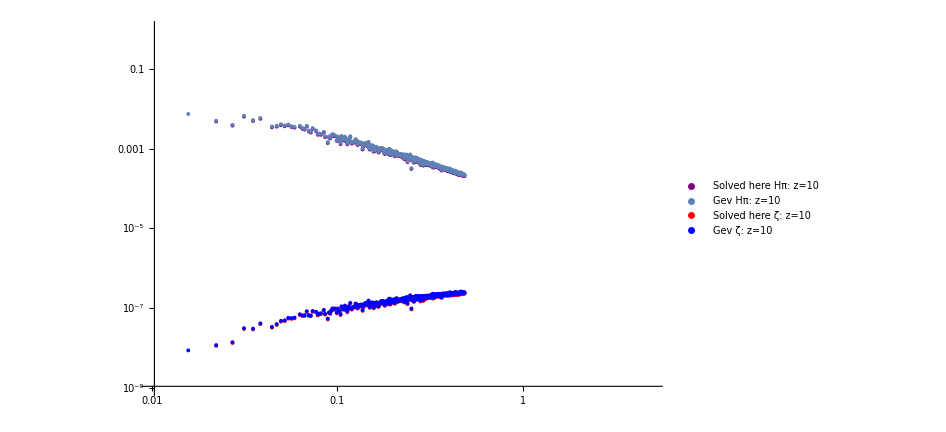

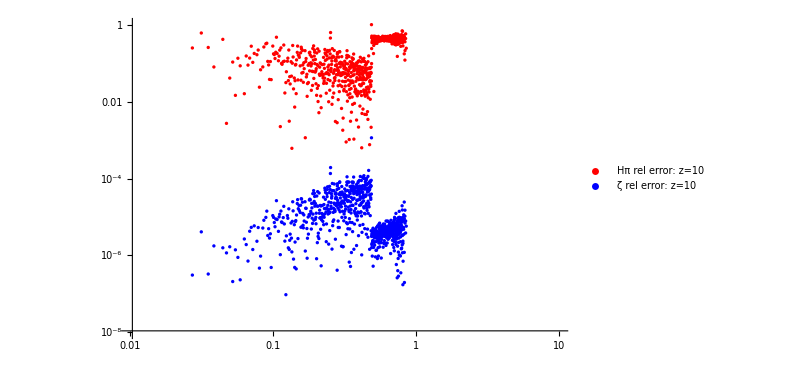

```mathematica
(*p1=ListLogLogPlot[MatSolz100[[All,{1,2}]],PlotStyle->{Blue,Line,PointSize[0.004]},PlotLegends->{"Solved here Ηπ: z=100"},ImageSize->900,PlotRange->{{10^-2,10},{10^-7,10^0}}];
p2=ListLogLogPlot[MatSolz10[[All,{1,2}]],PlotStyle->{Purple,Line,PointSize[0.004]},ImageSize->700,PlotLegends->{"Solved here Ηπ: z=10"},PlotRange->{{10^-2,5},{10^-9,10^0}}];
pζ1=ListLogLogPlot[MatSolz100[[All,{1,3}]],PlotStyle->{Black,Line,PointSize[0.004]},PlotLegends->{"Solved here ζ: z=100"},ImageSize->900,PlotRange->{{10^-2,10},{10^-12,10^-2}}];
pζ2=ListLogLogPlot[MatSolz10[[All,{1,3}]],PlotStyle->{Red,Line,PointSize[0.004]},ImageSize->900,PlotLegends->{"Solved here ζ: z=10"},PlotRange->{{10^-2,5},{10^-12,10^-6}}];
(*p1=ListLogLogPlot[MatSolz100[[All,{1,2}]],PlotStyle->{Green,Line,PointSize[0.004]},PlotLegends->{"Solved here π: z=100"},ImageSize->400,PlotRange->{{10^-4,10},{10^-6,1}}];*)
pGev100=ListLogLogPlot[GevPowerDataz100[[All,{1,2}]],PlotStyle->{Green,Line,PointSize[0.004]},PlotLegends->{"Gev Ηπ: z=100"},ImageSize->600];
pGev10=ListLogLogPlot[GevPowerDataz10[[All,{1,2}]],PlotStyle->{Maroon,Line,PointSize[0.004]},PlotLegends->{"Gev Ηπ: z=10"},ImageSize->600];
pζGev100=ListLogLogPlot[GevPowerDataz100[[All,{1,3}]],PlotStyle->{Brown,Line,PointSize[0.004]},PlotLegends->{"Gev ζ: z=100"},ImageSize->600];
pζGev10=ListLogLogPlot[GevPowerDataz10[[All,{1,3}]],PlotStyle->{Blue,Line,PointSize[0.004]},PlotLegends->{"Gev ζ: z=10"},ImageSize->600];
perrorπ=ListLogLogPlot[Errorπ[[All,{1,2}]],PlotStyle->{Red,Line,PointSize[0.004]},PlotLegends->{" Ηπ rel error: z=10"},ImageSize->600,PlotRange->{{10^-2,10},{10^-8,10^0}}];
perrorζ=ListLogLogPlot[Errorζ[[All,{1,2}]],PlotStyle->{Blue,Line,PointSize[0.004]},PlotLegends->{" ζ  rel error: z=10"},ImageSize->600];
Show[p1,pGev100,pζ1,pζGev100]
Show[p2,pGev10,pζ2,pζGev10]
Show[perrorπ,perrorζ]*)
```